```mathematica
Quit[];
```

-Need to project out π^+π^- state for diagrams ending in a charged pion loop in composite diagrams!
-Need to include triangle diagrams with 4π vertex at the end, not just the ρππ vertex!

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True]
```

## Load packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

Optional::opdef: The default value for the optional argument TraditionalForm`cc1_ : DiracGamma(h : 6 | 7)\ cc2_. contains a pattern.

General::stop: Further output of Optional :: opdef will be suppressed during this calculation.

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

# Compute some things

## Diagram and amplitude utilities

```mathematica
Pr=ChiralityProjector[1]//DiracSimplify[#,DiracSubstitute67->True]&;
Pl=ChiralityProjector[-1]//DiracSimplify[#,DiracSubstitute67->True]&;
```

### Abbreviations for states

```mathematica
stateA=V[1];
stateZ=V[2];
stateAux=V[5];
statel=F[4];
stateuq=F[7];
statedq=F[10];
```

### Functions for generating diagrams

```mathematica
exclusions={stateAux};

fcModelName="SMChi";

model={fcModelName<>"/"<>fcModelName,"UnitarySM"};
genericModel={"Lorentz","UnitaryLorentz",fcModelName<>"/"<>fcModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> {3,4}];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> exclusions]
]
```

```mathematica
paintDiags[diags_]:=Paint[diags,ColumnsXRows-> {Length[diags],1},SheetHeader->None,ImageSize-> {Length[diags]150,150}];
```

### Functions for creating amplitudes

```mathematica
createAmp[diags_,inmomenta_,outmomenta_,lorentzIndices_:{μ,ν,ρ,σ,α,β}]:=Module[{inOutStates,amp},

(*Compute the diagram*)
amp=CreateFeynAmp[diags, PreFactor->-ⅈ,Truncated-> True];

amp=FCFAConvert[amp,
IncomingMomenta-> inmomenta,
OutgoingMomenta-> outmomenta,
LoopMomenta->{l}, 
UndoChiralSplittings->True,
List->False,
SMP-> True,
LorentzIndexNames-> lorentzIndices,
ChangeDimension-> D,
FinalSubstitutions-> M$FACouplings,
SUNFIndexNames->{i,j,k,l,m,n},
SUNIndexNames->{a,b,c,d},
DropSumOver->True];

amp=DiracSimplify[amp,DiracSubstitute67-> True]
]
```

### Functions for extracting loop coefficients and integrals

The second and third arguments should be the names of lists that will stores the loop integral coefficients and loop integrals, respectively.

```mathematica
LoopIntCoeffSplit[amp_,LoopCoeffList_,LoopIntList_]:=Block[{list1,list2,list3,list4},

list1=List@@(amp//Expand);
list2=list1//ReplaceAll[#,DiracGamma[__]:>1]&//Calc;
list2=list2//ReplaceAll[#,{Pair[__]:>1,FeynAmpDenominator[__]:>1}]&;
list3=Table[list1⟦i⟧/list2⟦i⟧,{i,Length[list1]}];

LoopCoeffList=list2;

LoopIntList=list3;
]

NumPropSplit[LoopIntsList_]:=Block[{loopints,proplist,numlist,i,listprops,strprops,strnum,str,list},
(* initialize the list to zero *)
list={};

loopints=LoopIntsList//FeynAmpDenominatorSplit//MomentumCombine;

(* generate the entire list from LoopInts*)
numlist=Table[If[(SelectNotFree[loopints⟦k⟧,Pair]//ReplaceAll[#,Pair[__]:>0]&)==0,SelectNotFree[loopints⟦k⟧,Pair],1]//ReplaceAll[#,
{Pair[Momentum[a_,D],Momentum[b_,D]]:>StringJoin[ToString[a],"(mu)*",ToString[b],"(mu)"]}]&,
{k,Length[loopints]}];

proplist=Table[Cases2[loopints⟦k⟧,FeynAmpDenominator]//ReplaceAll[#,FeynAmpDenominator[PropagatorDenominator[Momentum[a_,D],b_]]:>a^2-b^2]&,{k,Length[loopints]}];


(* split the numerators and propagators *)
For[i=1,i≤Length[proplist],i++,

Clear[str,strprops,strnum];

strprops=StringJoin["propagators=[",StringDrop[StringJoin[Map[StringJoin["'",ToString[#,InputForm],"',"]&,Table[proplist⟦i,j⟧,{j,Length[proplist⟦i⟧]}]]],-1],"]"];

strnum=StringJoin["numerator='",ToString[numlist⟦i⟧],"'"];

str={strprops,strnum};

AppendTo[list,str];
];
list
]
```

### Functions for performing tensor/loop integral simplifications

```mathematica
smartTID[amp_]:=Module[{loopCoeffList,loopIntList,loopIntListNoDupes,loopIntListNoDupesTID,dupeLoopIntIndices,loopCoeffListNoDupes},
(* Split the amplitude *)
LoopIntCoeffSplit[amp,loopCoeffList,loopIntList];

(* Find unique integrals to be evaluated by TID *)
loopIntListNoDupes=DeleteDuplicates[loopIntList];
(* Apply TID to the unique loop integrals *)
loopIntListNoDupesTID=TID[#,l,ToPaVe->True]&/@loopIntListNoDupes;

(* Find indices of duplicates in list of unique loop integrals *)
dupeLoopIntIndices=Table[Position[loopIntListNoDupes,li]⟦1⟧⟦1⟧,{li,loopIntList}];

(* Sum coefficients for unique loop integrals *)
loopCoeffListNoDupes=Table[0,{i,Range[Length[loopIntListNoDupes]]}]; (* make list of 0s to store results *)
Table[loopCoeffListNoDupes⟦dupeLoopIntIndices⟦i⟧⟧+= loopCoeffList⟦i⟧,{i,Range[Length[loopCoeffList]]}];
loopCoeffListNoDupes=Simplify[loopCoeffListNoDupes];

(* Sum all the coefficients times their respective loop integrals *)
loopCoeffListNoDupes.loopIntListNoDupesTID
]
```

```mathematica
simplifyPaVeCoeffs[ampTID_]:=Module[{a0s,b0s,c0s,a0Terms,b0Terms,c0Terms},
(* Get all loop functions appearing in the amplitude *)
a0s=Cases[ampTID,(x___)f__A0:>f,Infinity]//DeleteDuplicates;
b0s=Cases[ampTID,(x___)f__B0:>f,Infinity]//DeleteDuplicates;
c0s=Cases[ampTID,(x___)f__C0:>f,Infinity]//DeleteDuplicates;

(* Get loop functions' coefficients *)
a0Terms=Table[a0 (ampTID//Coefficient[#,a0]&),{a0,a0s}]//Flatten//Total//Simplify;
b0Terms=Table[b0 (ampTID//Coefficient[#,b0]&),{b0,b0s}]//Flatten//Total//Simplify;
c0Terms=Table[c0 (ampTID//Coefficient[#,c0]&),{c0,c0s}]//Flatten//Total//Simplify;

(* Sum to return total amplitude *)
a0Terms+b0Terms+c0Terms
]
```

## Aux→ū u

```mathematica
diags=genDiags[{stateAux},{-stateuq,stateuq},1];
```

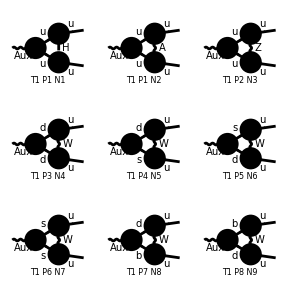

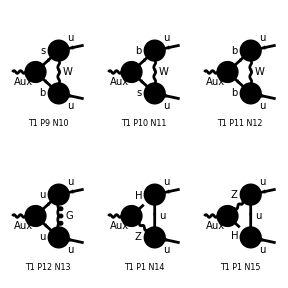

```mathematica
Paint[diags]
```

### Higgs-only diagram

```mathematica
amp=createAmp[diags//DiagramExtract[#,{1}]&,{P},{p1,p2}]/.{p1->0,p2->0}//Calc//Simplify;

ampTID=TID[amp,l,ToPaVe->True];
```

```mathematica
ampHiggsTIDL=ampTID.Pl/(GAD[μ].Pl)//Calc//PaXEvaluateUV[#,PaXImplicitPrefactor->1/(2π)^D]&//Simplify
ampHiggsTIDR=ampTID.Pr/(GAD[μ].Pr)//Calc//PaXEvaluateUV[#,PaXImplicitPrefactor->1/(2π)^D]&//Simplify
```

(Cu1 yup^2 δ_jk)/(64 π^2 ε_UV)

(Cq1 yup^2 δ_jk)/(64 π^2 ε_UV)

### Gluon diagram

```mathematica
amp=createAmp[diags//DiagramExtract[#,{13}]&,{P},{p1,p2}]/.{p1->0,p2->0}//Calc//Simplify;

ampTID=TID[amp,l,ToPaVe->True];

ampGluonL=ampTID.Pl/(GAD[μ].Pl)//Calc//PaXEvaluateUV[#,PaXImplicitPrefactor->1/(2π)^D]&//Simplify
ampGluonR=ampTID.Pr/(GAD[μ].Pr)//Calc//PaXEvaluateUV[#,PaXImplicitPrefactor->1/(2π)^D]&//Simplify
```

(Cq1 FAGS^2 C_F (γ^μ-γ^μ.(γ̄)^5) δ_jk)/(32 π^2 ε_UV)

(Cu1 FAGS^2 C_F (γ^μ.(γ̄)^5+γ^μ) δ_jk)/(32 π^2 ε_UV)